```mathematica
f[x_]:=
If[EvenQ[x],x/2,3x+1]
```

```mathematica
F[x_]:=({t=x};i=0;
While[t≠1,Print[t];t=f[t];i=i+1;If[t==1,Print[{t,Row[{Text["Number of Steps: "],i}]}]]])
```

```mathematica
G[x_]:=({u=x};If[u≠1,i=0;
While[u≠1,u=f[u];i++;];i,0])
```

```mathematica
H[x_]:=({v=x;h=0;};If[v≠1,i=0;
While[v≠1,If[h<v,h=v;j=i];v=f[v];i++;];
Column[{
Row[{Text["Total number of steps: "],i}],
Row[{Text["Maximum value of the process starting at this number: "],h}],
Row[{Text["Step value at maximum: "],j}]
}]
,
Column[{
Row[{Text["Total number of steps: "],0}],
Row[{Text["Maximum value of the process starting at this number: "],1}],
Row[{Text["Step value at maximum: "],0}]
}]
])
```

```mathematica
J[x_]:=(b=x;d=-1;
For[z=1,z≤b,z++,If[d<G[z],d=G[z]]];d
)
```

```mathematica
K[x_]:=(c=x;e=-1;
For[y=1,y≤c,y++,If[e<G[y],e=G[y];g=y]];
Column[{
Row[{Text["Process up to this number with the most steps: "],g}],
Row[{Text["Number of steps in this processes: "],e}]
}]
)
```

```mathematica
H[5]
```

Total number of steps: 5
Maximum value of the process starting at this number: 16
Step value at maximum: 1

```mathematica
q=G[101];
```

```mathematica
q
```

25

```mathematica
Manipulate[
Column[{
(*H[m],*)
K[m],
DiscretePlot[G[k],{k,1,m},Joined->False,ImageSize->500]
}]
,{m,5,1000}]
```

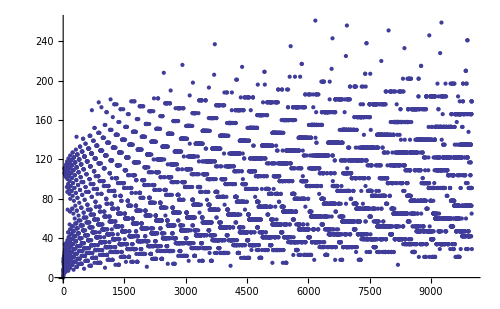

```mathematica
DiscretePlot[G[k],{k,1,10000},Filling->None,Joined->False,ImageSize->500]
```

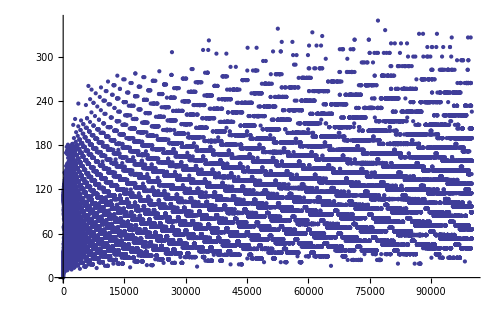

```mathematica
DiscretePlot[G[k],{k,1,100000},Filling->None,Joined->False,ImageSize->500]
```

```mathematica
Manipulate[
Column[{
DiscretePlot[J[k],{k,1,m},Joined->False,ImageSize->500]
}]
,
{m,5,1000}]
```